# Analytical Mechanics I

Basic Introductory calculations of Analytical Mechanics, following Marion Book.

## Part I: Linear Oscillations

## Simple Harmonic Motion

### Equation of motion

#### 1D Solution

```mathematica
Clear["Global`*"]
DSolve[x''[t]+ω^2 x[t]==0,x[t],t]
A=1; m=1; k =1;
ω=√(k/m);
x[t_,ϕ_]:= A* Cos[ω*t-ϕ]
Manipulate[Plot[{x[t,ϕ]},
		{t,0,(2Pi/(k/m)^(1/2))},
		(*PLotting options*)
		PlotLabel->"1D Oscillation",
		AxesLabel->{"t","x(t)"},
		GridLines->Automatic],{ϕ,0,Pi}]
```

{{x[t]→C[1] Cos[t ω]+C[2] Sin[t ω]}}

#### 2D

```mathematica
Clear["Global`*"]
A = 1; B=1; 
x[t_,ωx_,ϕx_] := A Cos[ωx t-ϕx]
y[t_,ωy_,ϕy_] := B Cos[ωy t-ϕy]
Manipulate[ParametricPlot[{x[t,ωx,ϕx],y[t,ωy,ϕy]},
		{t,0,tend},
		(*PLotting options*)
		AxesLabel->{"x(t)","y(t)"},
		PlotLabel->"2D Oscillation",
		AxesOrigin->Automatic,
		PlotLegends -> {"Ph diff:"+(ϕx-ϕy), "Omeg ratio:" (ωy/ωx)}],
                    {tend,100,1000},{ωx,1,10},
                    {ϕx,0,Pi},{ωy,2,10},{ϕy,0,Pi}]
```

#### 3D

```mathematica
Clear["Global`*"]
A = 1; B=1; c=1;
x[t_,ωx_,ϕx_] := A Cos[ωx t-ϕx]
y[t_,ωy_,ϕy_] := B Cos[ωy t-ϕy]
z[t_,ωz_,ϕz_] := c Cos[ωz t-ϕz]
Manipulate[ParametricPlot3D[{x[t,ωx,ϕx],y[t,ωy,ϕy],z[t,ωz,ϕz]},
		{t,0,tend},
		(*PLotting options*)
		AxesLabel->{"z(t)","y(t)","x(t)"},
		PlotLabel->"3D Ocillation",
		AxesOrigin->Automatic],{tend,100,1000},
		{ωx,1,10},{ωy,1,10},{ωz,1,10},
		{ϕx,0,Pi},{ϕy,0,Pi},{ϕz,0,Pi}]
```

### Phase space

```mathematica
Clear["Global`*"]
A=1;
ω[k_,m_] :=√(k/m);
τ[k_,m_]:=(2 Pi)/ω[k,m];
x[t_,k_,m_]:= A* Sin[ω[k,m]*t]
v[t_,k_,m_] := D[x[t,k,m],t]
Manipulate[ParametricPlot[{x[t,k,m],v[t0,k,m]/. t0->t},
		{t,0,τ[k,m]},
		(*PLotting options*)
		AxesLabel->{"x","v"},
		PlotLabel->"Phase Space",
		GridLines->Automatic,Frame->True], {k,1,10},{m,1,10}]
```

### Mechanical Energy

#### As a function of time

1/4

1/4

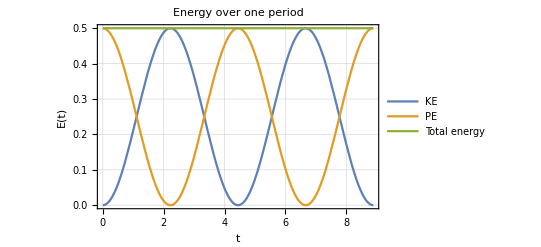

```mathematica
Clear["Global`*"]
A=1; k=1; m=2;
ω=√(k/m);
τ=(2 π)/ω;
x[t_]:= A* Cos[ω*t];
v[t_] := D[x[t],t];
KE[t_]:=1/2 m v[t]^2;
PE[t_]:=1/2 k x[t]^2;
KEtavg =1/τ Integrate[KE[t],{t,0,τ}]
PEtavg =1/τ Integrate[PE[t],{t,0,τ}]
Plot[{KE[t0]/. t0->t,PE[t0]/. t0->t, KE[t0]+PE[t0] /. t0->t},
		{t,0,τ},
		(*PLotting options*)
		AxesLabel->{"t","E(t)"},
		PlotLabel->"Energy over one period",
		GridLines->Automatic,
		PlotLegends -> {"KE","PE","Total energy"},Frame->True]
```

#### As a function of space

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

2 v^2+x^2==1

1/3

1/6

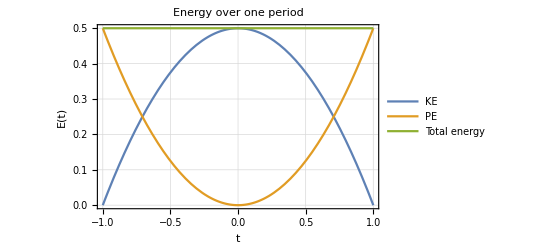

```mathematica
Clear["Global`*"]
A=1; k=1; m=2;
ω=√(k/m);
τ:=(2 π)/ω;

x[t_]:= A* Cos[ω*t];
v[t_] := D[x[t],t];
Eliminate[{v== v[t],x==x[t]},t]//FullSimplify
KE[x_]:= 1/2 m ω^2(A^2-x^2) 
PE[x_]:=1/2 k x^2;
KEsavg =1/A Integrate[KE[x],{x,0,A}]
PEsavg =1/A Integrate[PE[x],{x,0,A}]
Plot[{KE[x0]/. x0->x,PE[x0]/. x0->x, KE[x0]+PE[x0] /. x0->x},
		{x,-A,A},
		(*PLotting options*)
		AxesLabel->{"t","E(t)"},
		PlotLabel->"Energy over one period",
		GridLines->Automatic,
		PlotLegends -> {"KE","PE","Total energy"},Frame->True]
```

```mathematica
Manipulate[Plot[{0.5m ((k/m)^0.5)^2 (A^2-x^2),
		0.5k x^2, 0.5m (A(k/m)^0.5)^2(A^2-x^2) + 0.5k x^2},
		{x,-A,A},
		(*PLotting options*)
		AxesLabel->{"x","E(x)"},
		PlotLabel->"Energy over one period",
		GridLines->Automatic,
		PlotLegends -> {"KE(t)","PE(t)","KE+PE"}],{m,1,100},{k,1,10},{A,1,10}]
```

## Damped Oscillation

### Equation of motion

```mathematica
Clear["Global`*"]
DSolve[x''[t]+2B*x'[t]+w0^2*x[t]==0,x[t],t]
```

{{x[t]→ⅇ^(t (-B-√(B^2-w0^2))) C[1]+ⅇ^(t (-B+√(B^2-w0^2))) C[2]}}

### Under-damped case (ω > β)

#### Solution

```mathematica
Clear["Global`*"]
A=1; ϕ=0;
ω[k_,m_] :=√(k/m);
decay[t_,β_]:= A ⅇ^(-β t) ;
x[t_,β_,k_,m_] :=decay[t,β]A Cos[√(ω[k,m]^2-β^2)t+ϕ];
decrementofmotion[β_,k_,m_] := (A ⅇ^(-β t))/(A ⅇ^(-β (t+(2π)/ω[k,m])))//FullSimplify;
Manipulate[Plot[{x[t,β,k,m],decay[t,β]},{t,0,time},
(*PLotting options*)
		AxesLabel->{"t","x(t)"},
		GridLines->Automatic,
		PlotLabel->"Under-damped "+ decrementofmotion[β,k,m],
		PlotLegends -> {"Oscillation","Decaying rate"},Frame->True],
{time,1,100},{β,1,9},{m,1,2},{k,100,1000}]
```

#### Mechanical Energy

```mathematica
Clear["Global`*"]
ϕ=0; A=1;
ω[k_,m_] :=√(k/m);
x[t_,β_,k_,m_] :=A ⅇ^(-β t) Cos[√(ω[k,m]^2-β^2)t+ϕ]
v[t_,β_,k_,m_] :=D[ A ⅇ^(-β t) Cos[√(ω[k,m]^2-β^2)t+ϕ],t]
KE[t_,β_,k_,m_] := 1/2 m v[t,β,k,m]^2;
PE[t_,β_,k_,m_] := 1/2 m ω[k,m]^2 x[t,β,k,m]^2;
dEdt[t_,β_,k_,m_] :=D[PE[t,β,k,m]+KE[t,β,k,m],t];
Manipulate[
Row[
Plot[{PE[t,β,k,m],KE[t0,β,k,m]/.t0->t,PE[t,β,k,m]+KE[t0,β,k,m]/.t0->t},
{t,0,time},
AxesLabel->{"t","E(t)"},
PlotLabel->"Energy",
GridLines->Automatic,
PlotLegends -> {"PE","KE","Total"},ImageSize->Medium,Frame->True],

Plot[dEdt[t0,β,k,m]/.t0->t,{t,0,time},
PlotLabel->"Energy",
ImageSize->Medium,Frame->True]
],
{time,1,10},{β,1,9},{k,50,100},{m,1,2}]
```

#### Phase space

```mathematica
Clear["Global`*"]
ω[k_,m_] :=√(k/m);ϕ=0; A=1;
x[t_,β_,k_,m_] :=A ⅇ^(-β t)A Cos[√(ω[k,m]^2-β^2)t+ϕ];
v[t_,β_,k_,m_] :=D[ A ⅇ^(-β t) Cos[√(ω[k,m]^2-β^2)t+ϕ],t]
Manipulate[ParametricPlot[{x[t,β,k,m]*10,v[t0,β,k,m]/.t0->t},
		{t,0,tend},
		AxesLabel->{"x(t)","v(t)"},
		PlotLabel->"Phase Diagram for under-damped oscillator",
		GridLines->Automatic,
		Frame->True],{tend,1,10},{m,1,2},{k,100,1000},{β,1,9}]
```

### Critically-damped case (ω = β)

#### Solution

```mathematica
Clear["Global`*"]
x[t_,β_,A_,c_] :=(A +c t)ⅇ^(-β t) 
Manipulate[Plot[{x[t,β,A,c],A +c t},{t,0,tend},
(*PLotting options*)
		AxesLabel->{"t","x(t)"},
		PlotLabel->"Critically-damped",
		GridLines->Automatic,
		PlotLegends -> {"Decaying","Line amplitiude"}],{tend,1,10},{β,1,10},{A,1,10},{c,1,10}]
```

### Over-damped case (ω < β)

#### Solution

```mathematica
Clear["Global`*"]
A1=1;A2=1;
ω[k_,m_] :=√(k/m);
x[t_,β_,k_,m_] := ⅇ^(-β t)(A1 ⅇ^(√(β^2-ω[k,m]^2) t)+A2 ⅇ^(-√(β^2-ω[k,m]^2) t)) 
Manipulate[Plot[{x[t,β,k,m]},{t,0,tend},
		AxesLabel->{"t","x(t)"},
		PlotLabel->"Over-damped",
		GridLines->Automatic],{tend,1,10},{β,10,100},{k,1,9},{m,1,2}]
```

## Driven Oscillation

### Equation of motion

#### Solution

```mathematica
Clear["Global`*"]
DSolve[x''[t]+2β*x'[t]+ω^2(x[t]-x0)==A Cos[ωd t],x[t],t]//FullSimplify
```

{{x[t]→x0+ⅇ^(-t (β+√((β-ω) (β+ω)))) (C[1]+ⅇ^(2 t √(β^2-ω^2)) C[2])+(A (ω-ωd) (ω+ωd) Cos[t ωd]+2 A β ωd Sin[t ωd])/(ω^4-2 (-2 β^2+ω^2) ωd^2+ωd^4)}}

```mathematica
Clear["Global`*"]
Af=1;Ac=0.5;ϕc=0;
xc[t_,ω_,β_] := Ac ⅇ^(-β t) Cos[(ω^2-β^2)^(1/2)t-ϕc];
xp[t_,ωd_,ω_,β_] := Af/(√((ω^2-ωd^2)^2 + (2ωd β)^2)) Cos[ωd t-(2ωd β)/(ω^2-ωd^2)];
x[t_,ωd_,ω_,β_] := xc[t,ω,β]+xp[t,ωd,ω,β] ;
Manipulate[Plot[{xc[t,ω,β],xp[t,ωd,ω,β],x[t,ωd,ω,β]},{t,0,tend},
		AxesLabel->{"t","x(t)"},
		GridLines->Automatic,
		PlotLabel->"Diven damped oscillation",
		PlotLegends -> {"Complementray Sol","Particular Sol", "Final Sol"}, Frame->True],
		  {tend,10,100},{β,0.15,1},{ω,1,10},{ωd,2,10}]
```

### Resonance Phenomenon

#### Solving for Resonance Frequency

```mathematica
Clear["Global`*"]
Af=1;
Amp[ω_,ωd_,β_]:=Af/(√((ω^2-ωd^2)^2 + (2ωd β)^2));
Solve[D[Amp[ω,ωd,β],ωd]==0,ωd]
```

{{ωd→0},{ωd→-√(-2 β^2+ω^2)},{ωd→√(-2 β^2+ω^2)}}

#### Quality Factor

```mathematica
Clear["Global`*"]
Af=1; ω=1;
Amp[ω_,ωd_,β_]:=Af/(√((ω^2-ωd^2)^2 + (2ωd β)^2));
Manipulate[Plot[{Amp[ω,ωd,β],Amp[1,ωd,0.1],Amp[1,ωd,0.2],Amp[1,ωd,0.3]},{ωd,0.1,ωmax},
(*PLotting options*)
		AxesLabel->{"ω","Amp"},
		GridLines->Automatic,
		PlotLabel->"Measure of system's response to the driving force",
PlotLegends -> {"Aribitrary B","β=0.1","β=0.2","β=0.3"}],
{β,0.1,1},{ωmax,2,10}]
```

### Fourier series

#### Step function

```mathematica
Clear["Global`*"]
(*Define the function and half of the period*)
ω=1; p=ω/π;
f[t_]:=Piecewise[{{-1,-p<t<=0},{1,0<t<=p}}]
(*Coefficients*)
a0=(Integrate[f[t],{t,-p,p}])/2p
an=(Integrate[f[t]*Cos[t(n Pi)/p],{t,-p,p}])/p
bn=(Integrate[f[t]* Sin[t(n Pi)/p],{t,-p,p}])/p
(*Fourier Series*)
fourier[t_,N_]:=a0+ ∑_(n=1)^N an*Cos[t(n Pi)/p] + ∑_(n=1)^N bn*Sin[t(n Pi)/p]
Manipulate[Plot[{f[t],fourier[t,N]},{t,-p,p}],{N,1,100}]
```

0

0

-(2 (-1+Cos[n π]))/(n π)

#### Sawtooth function

```mathematica
Clear["Global`*"]
(*Define the function and half of the period*)
 ω=1;τ=(2 π)/ω; p= τ/2;
f[t_]:=Piecewise[{{t/τ,-p<t<=p}},0]
(*Coefficients*)
a0=(Integrate[f[t],{t,-p,p}])/2p
an=(Integrate[f[t]*Cos[t(n Pi)/p],{t,-p,p}])/p
bn=(Integrate[f[t]* Sin[t(n Pi)/p],{t,-p,p}])/p
(*Fourier Series*)
fourier[t_,N_]:=a0+ ∑_(n=1)^N an*Cos[t(n Pi)/p] + ∑_(n=1)^N bn*Sin[t(n Pi)/p]
Manipulate[Plot[{f[t],fourier[t,N]},{t,-p,p}],{N,1,100}]
```

0

0

(-n π Cos[n π]+Sin[n π])/(n^2 π^2)

### Response of the system for different forces

#### Heaviside force function

```mathematica
(*Equation of motion is simply*)
DSolve[x''[t]+2β*x'[t]+ω^2*x[t]==a,x[t],t]// FullSimplify
```

{{x[t]→a/ω^2+ⅇ^(-t (β+√(β^2-ω^2))) (C[1]+ⅇ^(2 t √(β^2-ω^2)) C[2])}}

```mathematica
Clear["Global`*"];
Ac=1; ω=1; β=0.1; ϕc=0; t0=0;
xc[t_,a_] := a/ω^2+ Ac ⅇ^(-β t) Cos[(ω^2-β^2)^(1/2)t-ϕc];
heaviside[t_,a_]:=Piecewise[{{0,t<t0},{a,t>t0}},0];
Manipulate[Plot[{heaviside[t,a],xc[t,a]},{t,0,10}],{a,1,10}]
```

## II: Non-linear Oscillations

## First Correction

### Symmetric Correction

```mathematica
Clear["Global`*"]
k=1; 
u[x_,c_]:= 1/2 k x^2 - c x^4
f[x_,c_]:=D[u[x,c],x]
Row[
Manipulate[

Row[
Plot[{u[x,0],u[x,c]},{x,-1,1},
		(*PLotting options*)
		ImageSize->Medium,
		PlotLabel->"Potentail Energy",
		AxesLabel->{"x","PE(x)"},
		PlotLegends -> {"Linear", "First correction"}],

Plot[{f[x0,0]/. x0->x,f[x1,c]/. x1->x},{x,-1,1},
		(*PLotting options*)
		ImageSize->Medium,		
		PlotLabel->"Force",
		AxesLabel->{"x","F(x)"},
		PlotLegends -> {"Linear", "First correction"}]
]
,{c,-1,1}]
]
```

Row[]

### Asymmetric Correction

```mathematica
Clear["Global`*"]
k=1; 
u[x_,c_]:= 1/2 k x^2 - c x^3

f[x_,c_]:=D[u[x,c],x]

Manipulate[
Row[
Plot[{f[x0,0]/. x0->x,f[x1,c]/. x1->x},{x,-1,1},
		(*PLotting options*)
ImageSize->Medium,		
PlotLabel->"Force",
		AxesLabel->{"x","F(x)"},
		PlotLegends -> {"Linear", "First correction"}],

Plot[{u[x,0],u[x,c]},{x,-1,1},
		(*PLotting options*)
		ImageSize->Medium,
		PlotLabel->"Potentail Energy",
		AxesLabel->{"x","PE(x)"},
		PlotLegends -> {"Linear", "First correction"}]
]
,{c,-1,1}]
```

## Interesting phenomenons

### Hysteresis k(x)

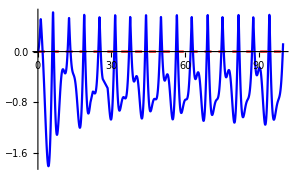
Row[-Graphics-,]

```mathematica
Clear["Global`*"]
(* Numericaly solve for k(x) *)
With[{k1=1,k2=80,m=1,w=1, B=0.1,a=0.5},s1 = NDSolve[{y[t]==x'[t],y'[t]+B*y[t]+If[x[t]<a,k1,k2-a(k2-k1)]/m x[t]==Cos[w t],x[0]==0.0, y[0]==0},{x,y},{t,400}]];
(*Visualize*)
tmax=20;
Row[
Plot[{0,x[t] /. s1},{t,0,100},PlotStyle-> {{Red,Dashed},Blue}, ImageSize->300]
(*Animation*),
ListAnimate@Table[
Plot[{0,x[t] /. s1},{t,0,tmax},PlotRange->{{0,tmax},{-2,2}}],{tmax,1,tmax,0.1}
]
]
```

```mathematica
A[x_]:=Piecewise[{{F/(√((k1-m w^2)^2 + (2 B w)^2)),x<a},{F/(√((k2-m w^2)^2 + (2 B w)^2)),x>a}}];
ph[x_]:=Piecewise[{{(B w)/(k1-m w^2),x<a},{(B w)/(k2-m w^2),x>a}}];

sol[t_,x_]:=Piecewise[{{A[x] * Cos[w t-ph[x]],x<a},{a(k2-k1)+A[x] * Cos[w t-ph[x]],x>a}}];
Manipulate[Plot[{a,sol[t,x]},{t,0,4}],{x,0,10}]
```

### Van Pol Equation damping (x)

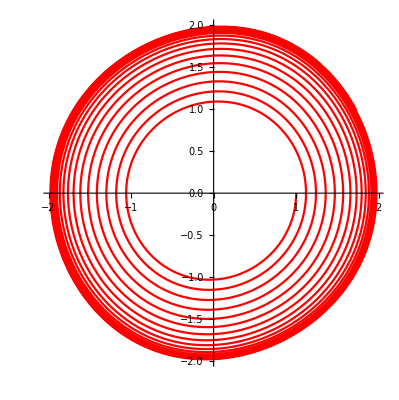

```mathematica
μ= 0.05; a = 1; ω=1; tmax = 100;
(* Initial conditions: x[0]== 1.50 and speed = 0 *)
s1=NDSolve[{x'[t]==y[t],y'[t]+μ (x[t]^2-a^2)y[t]+ ω^2 x[t]==0,x[0]== 1,y[0]==0},{x,y},{t,tmax}];
p1 =ParametricPlot[Evaluate[{x[t],y[t]}/.s1],{t,0,tmax},PlotStyle-> Red,PlotRange->All,LabelStyle->18];
Show[p1]
```

### Driven Non-linear Pendulum

#### Description

The torque around the pivot point 
-Graphics-

dividing by  I = m l^2
-Graphics-

We cast it into the dimensionless form by dividing by ω_0^2=g/l

-Graphics-

-Graphics-    -Graphics-

#### Solving the equation (Chaos at f0 = 0.6)

```mathematica
Clear["Global`*"]
c= 0.05; w=0.7; tmax = 700; f0 = 0.6(* f0 -> driving strength *);
s1=NDSolve[{x'[t]==y[t],y'[t]+c y[t]+ Sin[x[t]]-f0 Cos[w t]==0.0,x[0]== 1,y[0]==0},{x,y},{t,tmax}];
Row[
Manipulate[Plot[Evaluate[y[t]/.s1],{t,0,time},
AxesLabel->{"t'","y(t')"},
ImageSize->Medium,
Frame->True,
PlotLabel->"Solution"],{time,100,tmax}],
(*Phase diagram*)
Manipulate[ParametricPlot[Evaluate[{y[t],x[t]}/. s1],{t,0,time}, 
ImageSize->Small,
Frame->True,
AxesLabel->{"t'","y(t')"},
PlotLabel->"Phase Space"
],{time,100,tmax}]
]
```

Row[,]

#### Chaos Identification (Lyapunov Exponent)

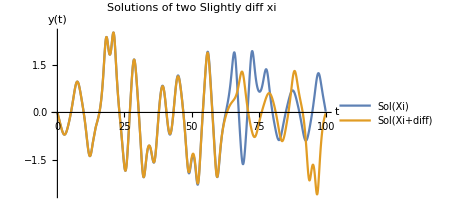
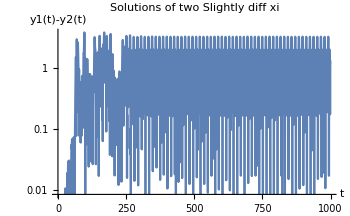
Row[-Graphics-,-Graphics-]

{6.37653}

```mathematica
Clear["Global`*"]
c= 0.05; w=0.7;f0 = 0.5;tmax=1000;diff = 0.001; init = 1.000;
s1=NDSolve[{x'[t]==y[t],y'[t]+c y[t]+ Sin[x[t]]-f0 Cos[w t]==0.0,x[0]== init,y[0]==0},{x,y},{t,tmax}];
s2=NDSolve[{xx'[t]==yy[t],yy'[t]+c yy[t]+ Sin[xx[t]]-f0 Cos[w t]==0.0,xx[0]== init+diff,yy[0]==0},{xx,yy},{t,tmax}];
Row[
Plot[{Evaluate[y[t]/. s1],Evaluate[yy[t]/. s2]},{t,0,tmax/10}, ImageSize->350,PlotLabel->"Solutions of two Slightly diff xi", AxesLabel->{"t","y(t)"},PlotLegends->{"Sol(Xi)","Sol(Xi+diff)"}],
LogPlot[{Abs[Evaluate[y[t]/. s1]-Evaluate[yy[t]/. s2]]},{t,0,tmax}, ImageSize->350,PlotLabel->"Solutions of two Slightly diff xi", AxesLabel->{"t","y1(t)-y2(t)"}]
]
(* Calaculating Exponent *)
λ=1/tmax∑_(t=1)^(tmax-1) Log[Abs[Evaluate[y[t]/. s1]-Evaluate[yy[t]/. s2]]/diff]
```

#### Bifurcation Diagram (Hard to identify the exact period due to my laziness, but doable)

{2.37412,2.61917,3.5366,3.11227,2.94312,1.52875,-0.304435,-1.64926,-1.51694,0.201296,1.90831,1.94758,1.60144,1.80738,0.985813,-0.568257,-1.1633,-0.192601,1.36667,1.97341,1.91316,2.61609,1.63693,-0.235674,-2.0001,-2.2186,-1.18863,-0.653038,-0.483505,-0.745903,-1.32059,-1.42735,-1.41726,-2.39276,-3.00551,-2.05253,-1.95736,-0.884406,0.570523,0.967053,-0.0603475,-1.32135,-1.4437,-1.04812,-0.899772,-0.89766,-0.769963,-0.456928,-0.319381,-0.489568}

{-2.52441,-1.02281,0.721082,0.686094,-1.07443,-2.64327,-4.10482,-4.61413,-4.20712,-2.45155,-0.99525,0.652795,0.575348,-1.14232,-2.60125,-4.12806,-4.57344,-4.12717,-2.36662,-0.96077,0.577028,0.451694,-1.21235,-2.56212,-4.16303,-4.54249,-4.04583,-2.3027,-0.916237,0.546439,0.368509,-1.27343,-2.55739,-4.21689,-4.53709,-3.97611,-2.27784,-0.863481,0.583847,0.351236,-1.32178,-2.59297,-4.28073,-4.55352,-3.92316,-2.27711,-0.808931,0.65172,0.365602,-1.36204}

{2.73252,5.48255,7.33984,7.38903,5.5129,2.41658,0.374912,-0.511977,0.840111,2.98843,5.66522,7.49619,7.45808,5.511,2.56943,0.238745,-0.887555,0.548186,2.99107,5.51711,7.33603,7.3419,5.41764,2.03865,0.239739,-0.0361133,1.61629,3.65095,6.49537,8.06914,7.81264,5.82849,2.54852,-0.160773,-1.38317,-1.39897,0.512045,2.56594,4.69074,4.37043,2.51558,-1.15951,-4.24628,-5.10948,-3.73241,-1.70601,1.70636,2.98757,3.42051,0.994241}

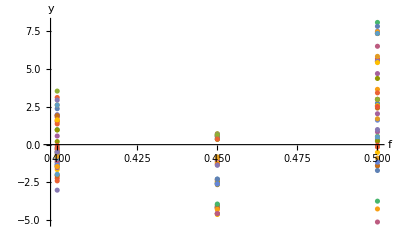

```mathematica
Clear["Global`*"]
c= 0.05; w=0.7;tmax=1000; init = 4.000;
fStep = 0.05; fStart =0.4; fEnd =0.5;

f = Range[fStart,fEnd,fStep];
fxList = 0f;

nb=50; (* nb = maximum number of bifurcations shown in the plot *)

sols =Table[0,{i, Length[f]},{j,nb}];
solt = Table[0,{i, tmax}];

(* Obtain the solution for multiple values of F *)
Do[

(* Solution for a given f *)
s1=NDSolve[{x'[t]==y[t],y'[t]+c y[t]+ Sin[x[t]]-f0 Cos[w t]==0.0,x[0]== init,y[0]==0},{x,y},{t,tmax}];
(* shrinking the time window + 20 *)
Do[solt[[i]] =First[y[i]/. s1],{i,tmax}];

(* Obtaining the last nb number (steady state sol)*)
sssol=solt[[-nb;;-1]];
sols[[f0]] =sssol;
Print[sssol]
,{f0,Length[f]}]

fyList = Table[{f[[f0]],sols[[f0,i]]},{i, nb},{f0,Length[f]}];
ListPlot[fyList, AxesLabel->{"f","y"},LabelStyle->18]
```

#### Poincare sections (Same problem as the previous subsection)

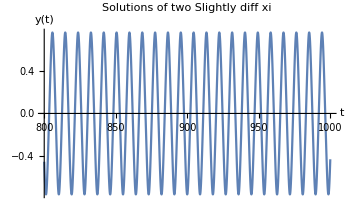
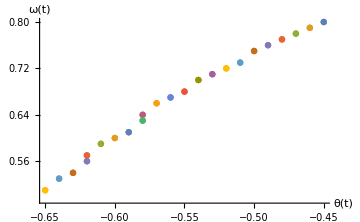
Row[-Graphics-,-Graphics-]

```mathematica
Clear["Global`*"]

(* The steady state period for this case is 9s *)
c= 0.05; w=0.7;f0 = 0.4;tmax=1000; init = 1.000;
s1=NDSolve[{x'[t]==y[t],y'[t]+c y[t]+ Sin[x[t]]-f0 Cos[w t]==0.0,x[0]== init,y[0]==0},{x,y},{t,tmax}];

(* Phase space plot after each period*)
p=9; tstart = 0.8*tmax;
yxList = Table[Round[{y[t],x[t]}/. s1,0.01],{t, tstart,tmax,p}];

Row[
Plot[{Evaluate[y[t]/. s1]},{t,tstart,tmax}, ImageSize->350,PlotLabel->"Solutions of two Slightly diff xi", AxesLabel->{"t","y(t)"}],
ListPlot[yxList, AxesLabel->{"θ(t)","ω(t)"},LabelStyle->18, ImageSize->Medium]
]
```

### Logistic map

#### Plot

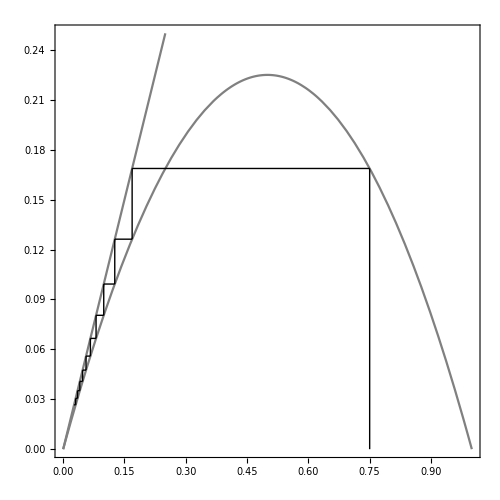

```mathematica
α=0.9; k=2; μ =0.9; x0=0.75; n=10;
Show[Plot[{μ x - μ x^2,x}, {x,0,1}, PlotStyle -> Gray,Frame->True,PlotRange-> {{0,1},{0,0.25}},AspectRatio -> 1],Graphics[Flatten[MapIndexed[{Line[{{#,If[#==x0,0,#]},{#,μ # - μ #^2}}],
Line[{{#, μ # - μ #^2},{μ # - μ #^2, μ # - μ #^2}}]}  & ,NestWhileList[μ # - μ #^2 &, x0, #1 ≠ μ #2 - μ #2^2 &, 2, n]]]],
ImageSize->{500,400},ImagePadding->{{20,10},{30,20}}]
```

#### Bifurcation Diagram

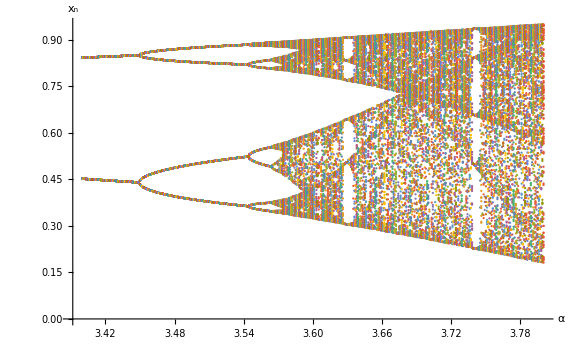

{2.99,3.447,3.545,3.565,3.569}

{0.004,0.02,0.098,0.457}

{4.66327,4.9,5.}

4.66327

```mathematica
αStep = 0.001; αStart =3.4; αEnd =3.8;
α = Range[αStart,αEnd,αStep];
αxList = 0α;

ns = 1500; (* ns = number of iteration. Larger values needed for stablitiy *)
nb=100; (* nb = maximum number of bifurcations shown in the plot *)

x =Table[0,{i, Length[α]},{j,nb}];
xn = Table[0,{i, ns}]; (* List of x values *)
xn[[1]]=0.5; (* Initial value of x *)

double=4;
doublealpha = Table[0,{i,0}];
AppendTo[doublealpha,2.99];
alphadiff = Table[0,{i,0}];
feigenbaum= Table[0,{i,0}];

Do[ 

Do[xn[[i]]=α[[nα]]xn[[i-1]](1-xn[[i-1]]),{i,2,ns}];

x[[nα]] =xn[[-nb;;-1]];

c = CountDistinct[Round[x[[nα]],0.00001]];

If[c == double,
AppendTo[doublealpha,α[[nα]]]; 
double=double*2;
];

,{nα,Length[α]}
];

αxList = Table[{α[[nα]],x[[nα,i]]},{nα,Length[α]},{i, nb}];
ListPlot[αxList, AxesLabel->{"α","x_n"},LabelStyle->18,ImageSize->Large]


(*Feigenbaum's number*)

For[i=Length[doublealpha],i>1,i--,
AppendTo[alphadiff,doublealpha[[i]]-doublealpha[[i-1]]];
]

For[i=Length[alphadiff],i>1,i--,
AppendTo[feigenbaum,alphadiff[[i]]/alphadiff[[i-1]]];
]

doublealpha
alphadiff
feigenbaum
feigenbaum[[1]]
```

## III: Gravitation

## Potential and Gravitational Field

### Point Masses

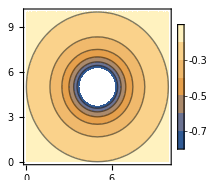
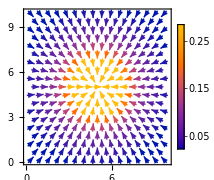
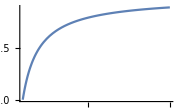
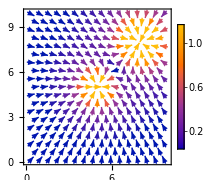
Column[Row[-Graphics-,-Graphics-,-Graphics-],Row[-Graphics-,-Graphics-,Null]]

```mathematica
Clear["Global`*"]
G=1;
x1 = 5;y1=5; m1=1;
x2 = 8;y2=8; m2=2;

phip[r_]:=(- G m1)/r;
phi1[x_,y_]:=(- G m1)/(((x-x1)^2+(y-y1)^2)^0.5);
phi2[x_,y_]:=(- G m2)/(((x-x2)^2+(y-y2)^2)^0.5);

f1[x_,y_]:={-D[phi1[x,y],x],-D[phi1[x,y],y]};
f2[x_,y_]:={-D[phi2[x,y],x],-D[phi2[x,y],y]};

Column[
Row[
ContourPlot[{phi1[x,y]},{x,0,10},{y,0,10}, PlotLegends->Automatic,ImageSize->Small],
VectorPlot[f1[x0,y0]/. x0->x/. y0->y,{x,0,10},{y,0,10}, PlotLegends->Automatic,ImageSize->Small],
Plot[phip[r],{r,1,10},ImageSize->Small]
],
Row[
ContourPlot[{phi1[x,y]},{x,0,10},{y,0,10}, PlotLegends->Automatic,ImageSize->Small],
VectorPlot[f1[x0,y0]+f2[x0,y0]/. x0->x/. y0->y,{x,0,10},{y,0,10}, PlotLegends->Automatic,ImageSize->Small],
]
]
```

### Uniform Rod

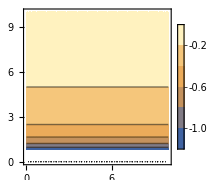
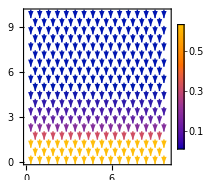
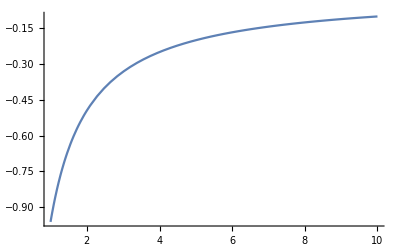
Row[-Graphics-,-Graphics-,-Graphics-]

```mathematica
Clear["Global`*"]
G=1;
 x1 =5; y1=5; m1=1; l=1;
phi[y_]:=(- G m1)/l Log[(√(l^2+4 y^2)+l)/(√(l^2+4 y^2)-l)];
f[y_]:={0,-D[phi[y],y]};
Row[
ContourPlot[phi[y],{x,0,10},{y,0,10}, ImageSize->Small,PlotLegends->Automatic],
VectorPlot[f[y0] /.y0->y,{x,0,10},{y,0,10}, PlotLegends->Automatic,ImageSize->Small],
Plot[phi[y],{y,1,10},ImageSize->{Automatic,Small}]
]
```

## Tides

### Moon effect on earth

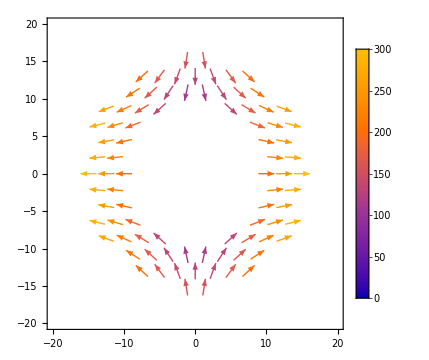
Column[Row[-Graphics-]]

```mathematica
Clear["Global`*"]
G=1; m=1; Mm=10; d=1; xe=8;ye=4; r=10; space=20;
tides[x_,y_] := Piecewise[{{{(2 G Mm m)/d^3 x,(- G Mm m)/d^3 y},r^2+135>=x^2+y^2>=r^2 },{{0,0},True}}];
Column[
Row[
VectorPlot[tides[x,y],{x,-space,space},{y,-space,space},PlotRange->All,ImageSize->Medium,PlotLegends->Automatic]
]
]
```

## V: Calculus of Variations

## Lagrange Multiplier

### Stationary area of a cylinder with fixed volume example

{106.283,75.1327,89.882,125.531,177.08,242.861,322.162,414.624,520.049,638.319}

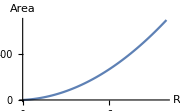
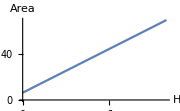
Row[-Graphics3D-,-Graphics-,-Graphics-]

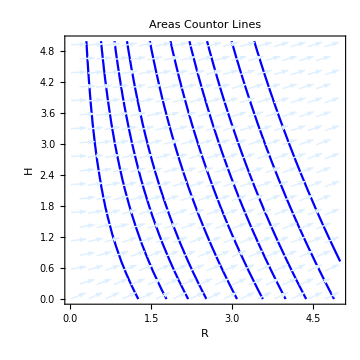
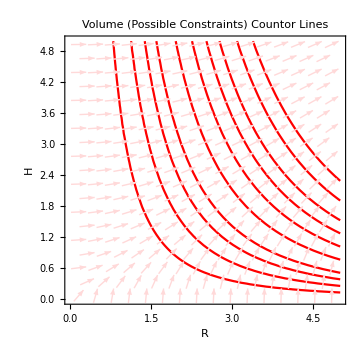
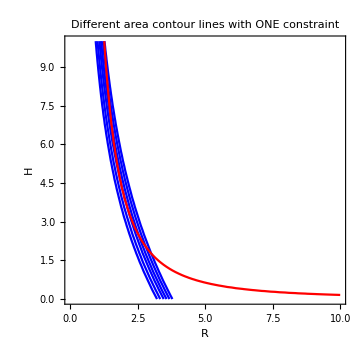
Row[-Graphics-,-Graphics-,-Graphics-]

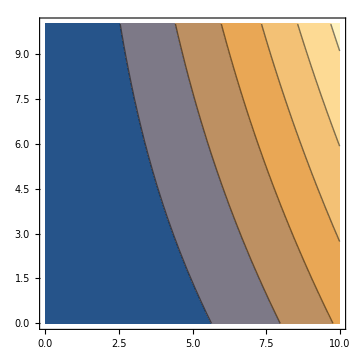
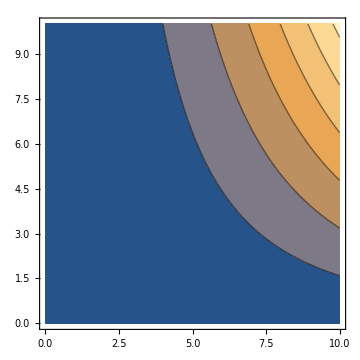
Row[-Graphics-,-Graphics-]

```mathematica
Clear["Global`*"]
volume=50;
range=10;

possibleareas = Table[0,{i,0}];
Do[AppendTo[possibleareas,N[2Pi(volume/(Pi R)+R^2)]],{R,range}]

possibleareas

A[R_,H_]:=2 π (R H + R^2);
g[R_,H_]:=π R^2 H ;
areaGrad = {D[A[R,H],R],D[A[R,H],H]};
volumeGrad = {D[g[R,H],R],D[g[R,H],H]};
(*Surface*)
Row[
Plot3D[{A[R,H]},{R,0,range},{H,0,range},ImageSize->Large,AxesLabel->{"R","H","Area"}],
With[{H=1},Plot[A[R,H],{R,0,range},ImageSize->Small,AxesLabel->{"R","Area"}]],
With[{R=1},Plot[A[R,H],{H,0,range},ImageSize->Small,AxesLabel->{"H","Area"}]]
]

Row[
(*Area Contour Lines*)
Show[
ContourPlot[{A[R,H] ==10,A[R,H] ==20,A[R,H] ==30,A[R,H] ==40,A[R,H] ==60,A[R,H] ==80,A[R,H] ==100,A[R,H] ==120,A[R,H] ==150,A[R,H] ==180},{R,0,5},{H,0,5}, 
ContourStyle->{Blue},
ImageSize->Medium,
FrameLabel->{"R","H"}],
VectorPlot[{areaGrad},{R,0,5},{H,0,5}, ImageSize->Medium, VectorColorFunction->None, VectorStyle-> LightBlue],
PlotLabel-> "Areas Countor Lines"
],
Show[
(*Volum Contour Lines*)
ContourPlot[{g[R,H] ==10,g[R,H] ==20,g[R,H] ==30,g[R,H] ==40,g[R,H] ==60,g[R,H] ==80,g[R,H] ==100,g[R,H] ==120,g[R,H] ==150,g[R,H] ==180},{R,0,5},{H,0,5}, 
ContourStyle->{Red},
ImageSize->Medium,
FrameLabel->{"R","H"}],
VectorPlot[{volumeGrad},{R,0,5},{H,0,5}, ImageSize->Medium,VectorColorFunction->None, VectorStyle-> LightRed],
PlotLabel-> "Volume (Possible Constraints) Countor Lines"
],
(*Extremum solution (The intersection point such that there is no change in area is the definition of extremum)*)
Show[
ContourPlot[{A[R,H]==65,A[R,H]==70,A[R,H]==75.39822368615503,A[R,H]==80.,A[R,H]==85.,A[R,H]==90.},{R,0,range},{H,0,range}, 
ContourStyle->{Blue},
ImageSize->Medium,
FrameLabel->{"R","H"}],
ContourPlot[{g[R,H] ==volume},{R,0,range},{H,0,range}, 
ContourStyle->{Red},
ImageSize->Medium,
FrameLabel->{"R","H"}],
PlotLabel-> "Different area contour lines with ONE constraint"
]
]

Row[
ContourPlot[{A[R,H]},{R,0,range},{H,0,range},ImageSize->Medium],
ContourPlot[{g[R,H]},{R,0,range},{H ,0,range},ImageSize->Medium]
]
```